## Convergence of the Mueller and Froyen kpoint selection methods

### Get Data

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
ma1=Import["data/Co_Mueller/out_1.csv","TSV"];
ma2=Import["data/Co_Mueller/out_2.csv","TSV"];
ma3=Import["data/Co_Mueller/out_3.csv","TSV"];
ma4=Import["data/Co_Mueller/out_4.csv","TSV"];
ma5=Import["data/Co_Mueller/out_5.csv","TSV"];
ma6=Import["data/Co_Mueller/out_6.csv","TSV"];
ma7=Import["data/Co_Mueller/out_7.csv","TSV"];
ma8=Import["data/Co_Mueller/out_8.csv","TSV"];
ma9=Import["data/Co_Mueller/out_9.csv","TSV"];
ma10=Import["data/Co_Mueller/out_10.csv","TSV"];
ma11=Import["data/Co_Mueller/out_11.csv","TSV"];
mv1=Import["data/V_Mueller/out_1.csv","TSV"];
mv2=Import["data/V_Mueller/out_2.csv","TSV"];
mv3=Import["data/V_Mueller/out_3.csv","TSV"];
mv4=Import["data/V_Mueller/out_4.csv","TSV"];
mv5=Import["data/V_Mueller/out_5.csv","TSV"];
mv6=Import["data/V_Mueller/out_6.csv","TSV"];
mv7=Import["data/V_Mueller/out_7.csv","TSV"];
mv8=Import["data/V_Mueller/out_8.csv","TSV"];
mv9=Import["data/V_Mueller/out_9.csv","TSV"];
mv10=Import["data/V_Mueller/out_10.csv","TSV"];
mv11=Import["data/V_Mueller/out_11.csv","TSV"];
mw1=Import["data/W_Mueller/out_1.csv","TSV"];
mw2=Import["data/W_Mueller/out_2.csv","TSV"];
mw3=Import["data/W_Mueller/out_3.csv","TSV"];
mw4=Import["data/W_Mueller/out_4.csv","TSV"];
mw5=Import["data/W_Mueller/out_5.csv","TSV"];
mw6=Import["data/W_Mueller/out_6.csv","TSV"];
mw7=Import["data/W_Mueller/out_7.csv","TSV"];
mw8=Import["data/W_Mueller/out_8.csv","TSV"];
mw9=Import["data/W_Mueller/out_9.csv","TSV"];
mw10=Import["data/W_Mueller/out_10.csv","TSV"];
mw11=Import["data/W_Mueller/out_11.csv","TSV"];
a1=Import["data/Co_Froyen/out_1.csv","TSV"];
a2=Import["data/Co_Froyen/out_2.csv","TSV"];
a3=Import["data/Co_Froyen/out_3.csv","TSV"];
a4=Import["data/Co_Froyen/out_4.csv","TSV"];
a5=Import["data/Co_Froyen/out_5.csv","TSV"];
a6=Import["data/Co_Froyen/out_6.csv","TSV"];
a7=Import["data/Co_Froyen/out_7.csv","TSV"];
a8=Import["data/Co_Froyen/out_8.csv","TSV"];
a9=Import["data/Co_Froyen/out_9.csv","TSV"];
a10=Import["data/Co_Froyen/out_10.csv","TSV"];
a11=Import["data/Co_Froyen/out_11.csv","TSV"];
v1=Import["data/V_Froyen/out_1.csv","TSV"];
v2=Import["data/V_Froyen/out_2.csv","TSV"];
v3=Import["data/V_Froyen/out_3.csv","TSV"];
v4=Import["data/V_Froyen/out_4.csv","TSV"];
v5=Import["data/V_Froyen/out_5.csv","TSV"];
v6=Import["data/V_Froyen/out_6.csv","TSV"];
v7=Import["data/V_Froyen/out_7.csv","TSV"];
v8=Import["data/V_Froyen/out_8.csv","TSV"];
v9=Import["data/V_Froyen/out_9.csv","TSV"];
v10=Import["data/V_Froyen/out_10.csv","TSV"];
v11=Import["data/V_Froyen/out_11.csv","TSV"];
w1=Import["data/W_Froyen/out_1.csv","TSV"];
w2=Import["data/W_Froyen/out_2.csv","TSV"];
w3=Import["data/W_Froyen/out_3.csv","TSV"];
w4=Import["data/W_Froyen/out_4.csv","TSV"];
w5=Import["data/W_Froyen/out_5.csv","TSV"];
w6=Import["data/W_Froyen/out_6.csv","TSV"];
w7=Import["data/W_Froyen/out_7.csv","TSV"];
w8=Import["data/W_Froyen/out_8.csv","TSV"];
w9=Import["data/W_Froyen/out_9.csv","TSV"];
w10=Import["data/W_Froyen/out_10.csv","TSV"];
w11=Import["data/W_Froyen/out_11.csv","TSV"];
afc1=Import["data/Co_AFLOW/out_1.csv","TSV"];
afc2=Import["data/Co_AFLOW/out_2.csv","TSV"];
afc3=Import["data/Co_AFLOW/out_3.csv","TSV"];
afc4=Import["data/Co_AFLOW/out_4.csv","TSV"];
afc5=Import["data/Co_AFLOW/out_5.csv","TSV"];
afc6=Import["data/Co_AFLOW/out_6.csv","TSV"];
afc7=Import["data/Co_AFLOW/out_7.csv","TSV"];
afc8=Import["data/Co_AFLOW/out_8.csv","TSV"];
afc9=Import["data/Co_AFLOW/out_9.csv","TSV"];
afc10=Import["data/Co_AFLOW/out_10.csv","TSV"];
afc11=Import["data/Co_AFLOW/out_11.csv","TSV"];
afv1=Import["data/V_AFLOW/out_1.csv","TSV"];
afv2=Import["data/V_AFLOW/out_2.csv","TSV"];
afv3=Import["data/V_AFLOW/out_3.csv","TSV"];
afv4=Import["data/V_AFLOW/out_4.csv","TSV"];
afv5=Import["data/V_AFLOW/out_5.csv","TSV"];
afv6=Import["data/V_AFLOW/out_6.csv","TSV"];
afv7=Import["data/V_AFLOW/out_7.csv","TSV"];
afv8=Import["data/V_AFLOW/out_8.csv","TSV"];
afv9=Import["data/V_AFLOW/out_9.csv","TSV"];
afv10=Import["data/V_AFLOW/out_10.csv","TSV"];
afv11=Import["data/V_AFLOW/out_11.csv","TSV"];
afw1=Import["data/W_AFLOW/out_1.csv","TSV"];
afw2=Import["data/W_AFLOW/out_2.csv","TSV"];
afw3=Import["data/W_AFLOW/out_3.csv","TSV"];
afw4=Import["data/W_AFLOW/out_4.csv","TSV"];
afw5=Import["data/W_AFLOW/out_5.csv","TSV"];
afw6=Import["data/W_AFLOW/out_6.csv","TSV"];
afw7=Import["data/W_AFLOW/out_7.csv","TSV"];
afw8=Import["data/W_AFLOW/out_8.csv","TSV"];
afw9=Import["data/W_AFLOW/out_9.csv","TSV"];
afw10=Import["data/W_AFLOW/out_10.csv","TSV"];
afw11=Import["data/W_AFLOW/out_11.csv","TSV"];
```

### Results

This is a plot of the error in the energy values of the Muellor and Froyen methods. The plot shows the log of the errors vs the number of irreducible kpoints used. The Red dots are the results of the Mueller method and the Blue are the results of the Froyen method.
As can be seen the Mueller method generally outperforms the Froyen method.

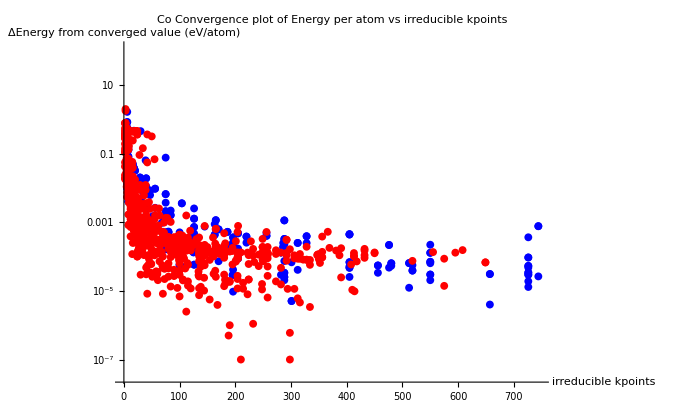

```mathematica
ListLogPlot[{a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,v1,v2,v3,v4,v5,v6,v7,v8,v9,v10,w1,w2,w3,w4,w5,w6,w7,w8,w9,w10,ma1,ma2,ma3,ma4,ma5,ma6,ma7,ma8,ma9,ma10,mv1,mv2,mv3,mv4,mv5,mv6,mv7,mv8,mv9,mv10,mw1,mw2,mw3,mw4,mw5,mw6,mw7,mw8,mw9,mw10},PlotStyle->Join[Table[Blue,{i,30}],Table[Red,{i,30}]], PlotLabel->"Co Convergence plot of Energy per atom vs irreducible kpoints",AxesLabel->{"irreducible kpoints","ΔEnergy from converged value (eV/atom)"}]
```

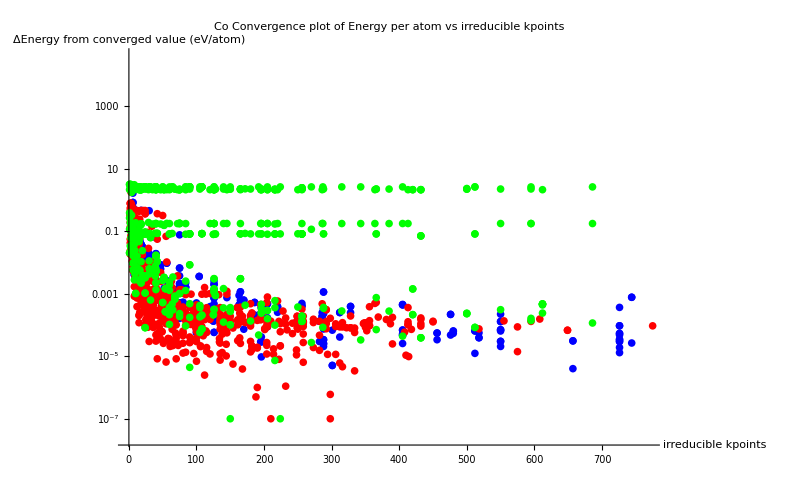

```mathematica
ListLogPlot[{a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,v1,v2,v3,v4,v5,v6,v7,v8,v9,v10,v11,w1,w2,w3,w4,w5,w6,w7,w8,w9,w10,w11,ma1,ma2,ma3,ma4,ma5,ma6,ma7,ma8,ma9,ma10,ma11,mv1,mv2,mv3,mv4,mv5,mv6,mv7,mv8,mv9,mv10,mv11,mw2,mw3,mw4,mw5,mw6,mw7,mw8,mw9,mw10,mw11,afc1,afc2,afc3,afc4,afc5,afc6,afc7,afc8,afc9,afc10,afc11,afw1,afw2,afw3,afw4,afw5,afw6,afw7,afw8,afw9,afw10,afw11,afv1,afv2,afv3,afv4,afv5,afv6,afv7,afv8,afv9,afv10,afv11},PlotStyle->Join[Table[Blue,{i,33}],Table[Red,{i,33}],Table[Green,{i,33}]], PlotLabel->"Co Convergence plot of Energy per atom vs irreducible kpoints",AxesLabel->{"irreducible kpoints","ΔEnergy from converged value (eV/atom)"}]
```

## Speed up from using the Mueller method compared to the Froyen method

### Get data

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
fc1=Import["data/Froyen_vs_Mueller/F_Co_1.csv","TSV"];
fc2=Import["data/Froyen_vs_Mueller/F_Co_2.csv","TSV"];
fc3=Import["data/Froyen_vs_Mueller/F_Co_3.csv","TSV"];
fc4=Import["data/Froyen_vs_Mueller/F_Co_4.csv","TSV"];
fc5=Import["data/Froyen_vs_Mueller/F_Co_5.csv","TSV"];
fc6=Import["data/Froyen_vs_Mueller/F_Co_6.csv","TSV"];
fc7=Import["data/Froyen_vs_Mueller/F_Co_7.csv","TSV"];
fc8=Import["data/Froyen_vs_Mueller/F_Co_8.csv","TSV"];
fc9=Import["data/Froyen_vs_Mueller/F_Co_9.csv","TSV"];
fc10=Import["data/Froyen_vs_Mueller/F_Co_10.csv","TSV"];fc11=Import["data/Froyen_vs_Mueller/F_Co_11.csv","TSV"];fv1=Import["data/Froyen_vs_Mueller/F_V_1.csv","TSV"];
fv2=Import["data/Froyen_vs_Mueller/F_V_2.csv","TSV"];
fv3=Import["data/Froyen_vs_Mueller/F_V_3.csv","TSV"];
fv4=Import["data/Froyen_vs_Mueller/F_V_4.csv","TSV"];
fv5=Import["data/Froyen_vs_Mueller/F_V_5.csv","TSV"];
fv6=Import["data/Froyen_vs_Mueller/F_V_6.csv","TSV"];
fv7=Import["data/Froyen_vs_Mueller/F_V_7.csv","TSV"];
fv8=Import["data/Froyen_vs_Mueller/F_V_8.csv","TSV"];
fv9=Import["data/Froyen_vs_Mueller/F_V_9.csv","TSV"];
fv10=Import["data/Froyen_vs_Mueller/F_V_10.csv","TSV"];
fv11=Import["data/Froyen_vs_Mueller/F_V_11.csv","TSV"];
fw1=Import["data/Froyen_vs_Mueller/F_W_1.csv","TSV"];
fw2=Import["data/Froyen_vs_Mueller/F_W_2.csv","TSV"];
fw3=Import["data/Froyen_vs_Mueller/F_W_3.csv","TSV"];
fw4=Import["data/Froyen_vs_Mueller/F_W_4.csv","TSV"];
fw5=Import["data/Froyen_vs_Mueller/F_W_5.csv","TSV"];
fw6=Import["data/Froyen_vs_Mueller/F_W_6.csv","TSV"];
fw7=Import["data/Froyen_vs_Mueller/F_W_7.csv","TSV"];
fw8=Import["data/Froyen_vs_Mueller/F_W_8.csv","TSV"];
fw9=Import["data/Froyen_vs_Mueller/F_W_9.csv","TSV"];
fw10=Import["data/Froyen_vs_Mueller/F_W_10.csv","TSV"];fw11=Import["data/Froyen_vs_Mueller/F_W_11.csv","TSV"];
ac1=Import["data/AFLOW_vs_Mueller/A_Co_1.csv","TSV"];
ac2=Import["data/AFLOW_vs_Mueller/A_Co_2.csv","TSV"];
ac3=Import["data/AFLOW_vs_Mueller/A_Co_3.csv","TSV"];
ac4=Import["data/AFLOW_vs_Mueller/A_Co_4.csv","TSV"];
ac5=Import["data/AFLOW_vs_Mueller/A_Co_5.csv","TSV"];
ac6=Import["data/AFLOW_vs_Mueller/A_Co_6.csv","TSV"];
ac7=Import["data/AFLOW_vs_Mueller/A_Co_7.csv","TSV"];
ac8=Import["data/AFLOW_vs_Mueller/A_Co_8.csv","TSV"];
ac9=Import["data/AFLOW_vs_Mueller/A_Co_9.csv","TSV"];
ac10=Import["data/AFLOW_vs_Mueller/A_Co_10.csv","TSV"];ac11=Import["data/AFLOW_vs_Mueller/A_Co_11.csv","TSV"];av1=Import["data/AFLOW_vs_Mueller/A_V_1.csv","TSV"];
av2=Import["data/AFLOW_vs_Mueller/A_V_2.csv","TSV"];
av3=Import["data/AFLOW_vs_Mueller/A_V_3.csv","TSV"];
av4=Import["data/AFLOW_vs_Mueller/A_V_4.csv","TSV"];
av5=Import["data/AFLOW_vs_Mueller/A_V_5.csv","TSV"];
av6=Import["data/AFLOW_vs_Mueller/A_V_6.csv","TSV"];
av7=Import["data/AFLOW_vs_Mueller/A_V_7.csv","TSV"];
av8=Import["data/AFLOW_vs_Mueller/A_V_8.csv","TSV"];
av9=Import["data/AFLOW_vs_Mueller/A_V_9.csv","TSV"];
av10=Import["data/AFLOW_vs_Mueller/A_V_10.csv","TSV"];
av11=Import["data/AFLOW_vs_Mueller/A_V_11.csv","TSV"];
aw1=Import["data/AFLOW_vs_Mueller/A_W_1.csv","TSV"];
aw2=Import["data/AFLOW_vs_Mueller/A_W_2.csv","TSV"];
aw3=Import["data/AFLOW_vs_Mueller/A_W_3.csv","TSV"];
aw4=Import["data/AFLOW_vs_Mueller/A_W_4.csv","TSV"];
aw5=Import["data/AFLOW_vs_Mueller/A_W_5.csv","TSV"];
aw6=Import["data/AFLOW_vs_Mueller/A_W_6.csv","TSV"];
aw7=Import["data/AFLOW_vs_Mueller/A_W_7.csv","TSV"];
aw8=Import["data/AFLOW_vs_Mueller/A_W_8.csv","TSV"];
aw9=Import["data/AFLOW_vs_Mueller/A_W_9.csv","TSV"];
aw10=Import["data/AFLOW_vs_Mueller/A_W_10.csv","TSV"];aw11=Import["data/AFLOW_vs_Mueller/A_W_11.csv","TSV"];
```

### Results

This following plots are of the speedup (ratio of Froyen to Muelller and AFLOW to Mueller number of irreducible kpoints) vs the error in the energy for Co, W, and V of cell sizes ranging from 1 to 10 atoms per cell. In all the following plots the Blue lines correspond to Co data, the Red  correspond to V data, and Green corresponds to W data.

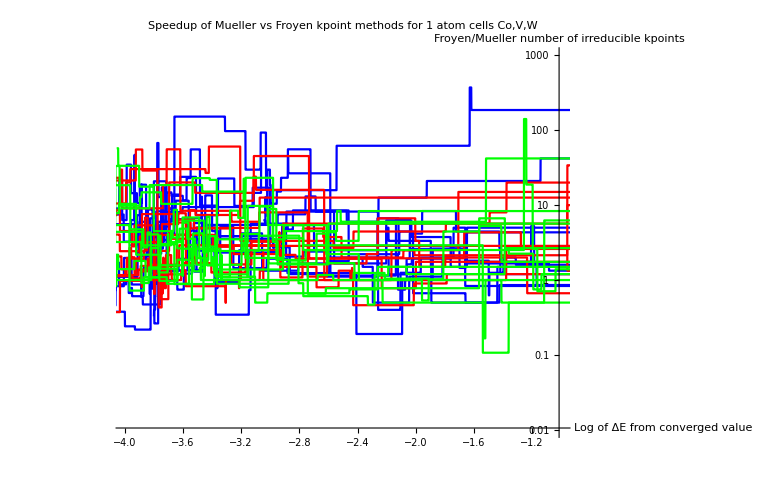

```mathematica
ListLogPlot[{fc1,fc2,fc3,fc4,fc5,fc6,fc7,fc8,fc9,fc10,fc11,fv1,fv2,fv3,fv4,fv5,fv6,fv7,fv8,fv9,fv10,fv11,fw1,fw2,fw3,fw4,fw5,fw6,fw7,fw8,fw9,fw10,fw11},Joined->True,PlotLabel->"Speedup of Mueller vs Froyen kpoint methods for 1 atom cells Co,V,W",AxesLabel->{"Log of ΔE from converged value","Froyen/Mueller number of irreducible kpoints"},PlotStyle->Join[Table[Blue,{i,11}],Table[Red,{i,11}],Table[Green,{i,11}]],PlotRange->{{-4,-1},{10^-2,10^3}}]
```

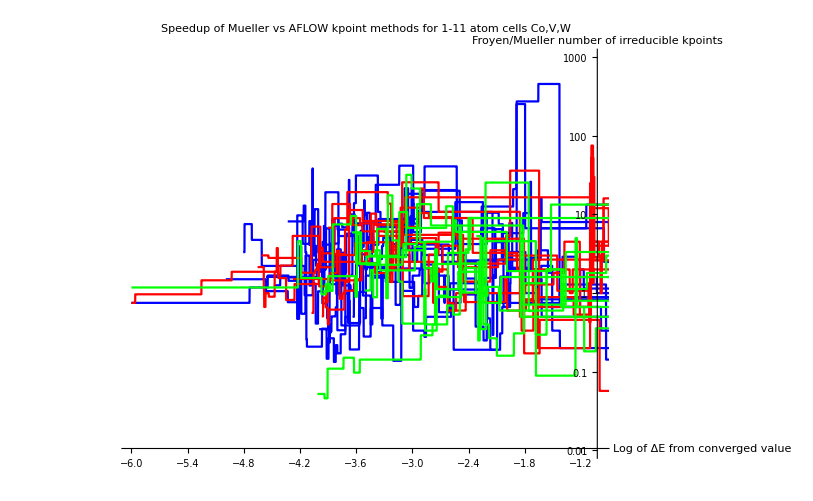

```mathematica
ListLogPlot[{ac1,ac2,ac3,ac4,ac5,ac6,ac7,ac8,ac9,ac10,ac11,av1,av2,av3,av4,av5,av6,av7,av8,av9,av10,av11,aw1,aw2,aw3,aw4,aw5,aw6,aw7,aw8,aw9,aw10,aw11},Joined->True,PlotLabel->"Speedup of Mueller vs AFLOW kpoint methods for 1-11 atom cells Co,V,W",AxesLabel->{"Log of ΔE from converged value","Froyen/Mueller number of irreducible kpoints"},PlotStyle->Join[Table[Blue,{i,11}],Table[Red,{i,11}],Table[Green,{i,11}]],PlotRange->{{-6,-1},{10^-2,10^3}}]
```

The differences in the “converged” value of the energy for each system varried by as much as 0.4 eV. In light of this the converged energy for the above plots was taken for each method independently and the errors are relative to those values.